```mathematica
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

```mathematica
Omega
```

{{ω[1,1],ω[1,2],ω[1,3],ω[1,4],ω[1,5],ω[1,6],0},{ω[1,2],ω[2,2],ω[2,3],ω[2,4],ω[2,5],ω[2,6],0},{ω[1,3],ω[2,3],ω[3,3],ω[3,4],ω[3,5],ω[3,6],0},{ω[1,4],ω[2,4],ω[3,4],ω[4,4],ω[4,5],ω[4,6],0},{ω[1,5],ω[2,5],ω[3,5],ω[4,5],ω[5,5],ω[5,6],0},{ω[1,6],ω[2,6],ω[3,6],ω[4,6],ω[5,6],ω[6,6],0},{0,0,0,0,0,0,Δ}}

```mathematica
(*l = 1*)
(*I2noise = Expand[1]
I2 = Expand[(lf[1])*(lf[2])]
I3 = Expand[(1)*lf[2]*(lf[3])]
I4 = Expand[(1)*(1)*(lf[3])*(lf[4])]*)

(*l=2*)
(*I2noise = Expand[(2*lf[1])*(2*lf[2])]
I2 = Expand[(lf[1]^2-1)*(lf[2]^2-1)]
I3 = Expand[2*lf[1]*lf[2]*(lf[3]^2-1)]
I4 = Expand[(2*lf[1])*(2*lf[2])*(lf[3]^2-1)*(lf[4]^2-1)]*)

(*l=3*)
(*I2noise = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)]
I2 = Expand[(lf[1]^3-3*lf[1])*(lf[2]^3-3*lf[2])]
I3 = Expand[(3*lf[1]^2-3)*lf[2]*(lf[3]^3-3*lf[3])]
I4 = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)*(lf[3]^3-3*lf[3])*(lf[4]^3-3*lf[4])]*)

(*l=4*)
I2noise = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])]
I2=Expand[(lf[1]^4-6*lf[1]^2+3)*(lf[2]^4-6*lf[2]^2+3)]
I3 = Expand[(4*lf[1]^3-12*lf[1])*lf[2]*(lf[3]^4-6*lf[3]^2+3)]
I4 = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])*(lf[3]^4-6*lf[3]^2+3)*(lf[4]^4-6*lf[4]^2+3)]

(*l=5*)
(*I3 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*lf[2]*(lf[3]^5-10*lf[3]^3+15*lf[3])]*)
(*I4 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*(5*lf[2]^4-30*lf[2]^2+15)*(lf[3]^5-10*lf[3]^3+15*lf[3])*(lf[4]^5-10*lf[4]^3+15*lf[4])]*)

(*l=6*)
(*I3 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*lf[2]*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)]*)
(*I4 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*(6*lf[2]^5-60*lf[2]^3+90*lf[2])*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)*(lf[4]^6-15*lf[4]^4+45*lf[4]^2-15)]*)
```

144 λ[1] λ[2]-48 λ[1]^3 λ[2]-48 λ[1] λ[2]^3+16 λ[1]^3 λ[2]^3

9-18 λ[1]^2+3 λ[1]^4-18 λ[2]^2+36 λ[1]^2 λ[2]^2-6 λ[1]^4 λ[2]^2+3 λ[2]^4-6 λ[1]^2 λ[2]^4+λ[1]^4 λ[2]^4

-36 λ[1] λ[2]+12 λ[1]^3 λ[2]+72 λ[1] λ[2] λ[3]^2-24 λ[1]^3 λ[2] λ[3]^2-12 λ[1] λ[2] λ[3]^4+4 λ[1]^3 λ[2] λ[3]^4

1296 λ[1] λ[2]-432 λ[1]^3 λ[2]-432 λ[1] λ[2]^3+144 λ[1]^3 λ[2]^3-2592 λ[1] λ[2] λ[3]^2+864 λ[1]^3 λ[2] λ[3]^2+864 λ[1] λ[2]^3 λ[3]^2-288 λ[1]^3 λ[2]^3 λ[3]^2+432 λ[1] λ[2] λ[3]^4-144 λ[1]^3 λ[2] λ[3]^4-144 λ[1] λ[2]^3 λ[3]^4+48 λ[1]^3 λ[2]^3 λ[3]^4-2592 λ[1] λ[2] λ[4]^2+864 λ[1]^3 λ[2] λ[4]^2+864 λ[1] λ[2]^3 λ[4]^2-288 λ[1]^3 λ[2]^3 λ[4]^2+5184 λ[1] λ[2] λ[3]^2 λ[4]^2-1728 λ[1]^3 λ[2] λ[3]^2 λ[4]^2-1728 λ[1] λ[2]^3 λ[3]^2 λ[4]^2+576 λ[1]^3 λ[2]^3 λ[3]^2 λ[4]^2-864 λ[1] λ[2] λ[3]^4 λ[4]^2+288 λ[1]^3 λ[2] λ[3]^4 λ[4]^2+288 λ[1] λ[2]^3 λ[3]^4 λ[4]^2-96 λ[1]^3 λ[2]^3 λ[3]^4 λ[4]^2+432 λ[1] λ[2] λ[4]^4-144 λ[1]^3 λ[2] λ[4]^4-144 λ[1] λ[2]^3 λ[4]^4+48 λ[1]^3 λ[2]^3 λ[4]^4-864 λ[1] λ[2] λ[3]^2 λ[4]^4+288 λ[1]^3 λ[2] λ[3]^2 λ[4]^4+288 λ[1] λ[2]^3 λ[3]^2 λ[4]^4-96 λ[1]^3 λ[2]^3 λ[3]^2 λ[4]^4+144 λ[1] λ[2] λ[3]^4 λ[4]^4-48 λ[1]^3 λ[2] λ[3]^4 λ[4]^4-48 λ[1] λ[2]^3 λ[3]^4 λ[4]^4+16 λ[1]^3 λ[2]^3 λ[3]^4 λ[4]^4

```mathematica
Psit =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->m,ω[2,2]->ρ,ω[2,3]->ρ,ω[3,3]->ρ} ;
Psis= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->q,ω[2,2]->ρ,ω[2,3]->m,ω[3,3]->q} ;
(*Psis = 0;*)
PhiHDtt = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[1,4]->m,ω[2,2]->q,ω[2,3]->m,ω[2,4]->m,ω[3,3]->ρ,ω[3,4]->ρ,ω[4,4]->ρ} ;
PhiHDss = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->q,ω[2,2]->q,ω[2,3]->q,ω[2,4]->q,ω[3,3]->q,ω[3,4]->q,ω[4,4]->q} ;
(*PhiHDss = 0;*)
PhiHDts = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->m,ω[2,2]->q,ω[2,3]->q,ω[2,4]->m,ω[3,3]->q,ω[3,4]->m,ω[4,4]->ρ} ;
(*PhiHDts = 0;*)
PhiHDnoise = IsserlisTheorem[I2noise] /. {ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
PhiGFt =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[2,2]->q,ω[2,3]->m,ω[3,3]->ρ} ;
PhiGFs= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[2,2]->q,ω[2,3]->q,ω[3,3]->q} ;
(*PhiGFs=0;*)
Riskss =IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->q,ω[2,2]->q};
(*Riskss = 0;*)
Risktt = IsserlisTheorem[I2] /.{ω[1,1]->ρ,ω[1,2]->ρ,ω[2,2]->ρ};
Riskts = IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
(*Riskts = 0;*)
Pinv = 1/ρ;
Qorthinv = 1/(q-m^2/ρ);
GFM = FullSimplify[(Psit-Psis)];
GFQ = FullSimplify[(PhiGFt-PhiGFs)];
GFQorth = FullSimplify[GFQ - m*Pinv*GFM];
HDQ = (PhiHDtt+PhiHDss-2*PhiHDts+Δ*PhiHDnoise);
mUpdate =γ*GFM
qUpdate = FullSimplify[2*γ*GFQ+γ^2*1/α*HDQ+γ^2*ind*(GFM*Pinv*GFM)+γ^2*ind*(GFQorth*Qorthinv*GFQorth)]
PopRisk = 1/2*(Riskss +Risktt-2*Riskts)
```

12 m γ (q (-18+5 (9-7 q) q)-18 (-1+q) ρ+15 (-1+q) ρ^2+4 m^2 (-3+5 ρ))

1/α 24 γ (4 m^3 γ Δ+6 m (-1+q) γ Δ (-1+ρ)+q (q (90 q (36+7 q (-36+q (117+11 q (-18+13 q)))) γ+(18+5 q (-9+7 q)) α (-1+6 ind q (18+5 q (-9+7 q)) γ))+6 (12 q (-18+5 q (15+7 q (-4+3 q))) γ+(-1+q) α (-1+12 ind q (18+5 q (-9+7 q)) γ)) ρ-3 (12 (-18+q (18+5 q (9+7 q (-4+3 q)))) γ+(-1+q) α (-1+12 ind (6+q (12+5 q (-9+7 q))) γ)) ρ^2-72 (15+5 q (-6+5 q)+3 ind (-1+q)^2 α) γ ρ^3+6 (35 (3+q (-6+5 q))+9 ind (-1+q)^2 α) γ ρ^4)+384 m^6 γ (ind α (-3+4 ρ)+5 (-3+7 ρ))+8 m^4 (α-36 (6+5 q (9+14 q (-4+5 q))) γ+180 (-2+5 q) γ ρ (-6+7 ρ)-12 ind α γ (18+q (-9+5 q (-9+7 q))-54 ρ+72 q ρ+3 (11-14 q) ρ^2))+12 m^2 (α (-1+ρ) (-1+2 q-12 ind q (-1+2 q) (18+5 q (-9+7 q)) γ-72 ind (-1+q) (-2+3 q) γ ρ+36 ind (-1+q) (-3+4 q) γ ρ^2)+12 γ (560 q^3 (-1+ρ)-525 q^4 (-1+ρ)+ρ (18+5 ρ (-9+7 ρ))+5 q^2 (45+ρ (-27+5 ρ (-9+7 ρ)))-4 q (9+ρ (9+5 ρ (-9+7 ρ))))))

1/2 (18-36 q+126 q^2-180 q^3+105 q^4-36 ρ+126 ρ^2-180 ρ^3+105 ρ^4-2 (9+72 m^2+24 m^4-18 q-72 m^2 q+9 q^2-18 ρ-72 m^2 ρ+36 q ρ+72 m^2 q ρ-18 q^2 ρ+9 ρ^2-18 q ρ^2+9 q^2 ρ^2))

```mathematica
mUpdateSpherical = Expand[FullSimplify[((m+mUpdate)/Sqrt[q+qUpdate]-m)/.{ρ->1,q->1}]]
```

-m+m/(√(1+(96 γ (2 (-1+m^4) α+48 (107+12 m^2+2 ind α+2 m^6 (20+ind α)-m^4 (159+4 ind α)) γ+m^3 γ Δ))/α))-(96 m γ)/(√(1+(96 γ (2 (-1+m^4) α+48 (107+12 m^2+2 ind α+2 m^6 (20+ind α)-m^4 (159+4 ind α)) γ+m^3 γ Δ))/α))+(96 m^3 γ)/(√(1+(96 γ (2 (-1+m^4) α+48 (107+12 m^2+2 ind α+2 m^6 (20+ind α)-m^4 (159+4 ind α)) γ+m^3 γ Δ))/α))

```mathematica
Series[mUpdateSpherical,{m,0,4}]
```

(-1+1/(√((α-192 α γ+493056 γ^2+9216 ind α γ^2)/α))-(96 γ)/(√((α-192 α γ+493056 γ^2+9216 ind α γ^2)/α))) m+(96 (α γ-288 γ^2-192 α γ^2+520704 γ^3+9216 ind α γ^3) m^3)/((α-192 α γ+493056 γ^2+9216 ind α γ^2) √((α-192 α γ+493056 γ^2+9216 ind α γ^2)/α))+(48 (-γ^2 Δ+96 γ^3 Δ) m^4)/((α-192 α γ+493056 γ^2+9216 ind α γ^2) √((α-192 α γ+493056 γ^2+9216 ind α γ^2)/α))+O[m]^5

-4.8 x+4.8 x^3

1/2 (48-48 x^4)

4.8 (-1/2+m^2/2)-4.8 (-1/4+m^4/4)

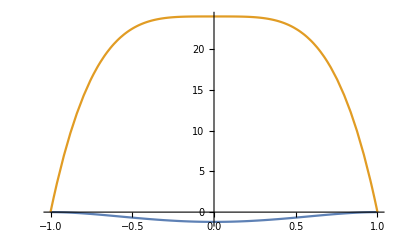

```mathematica
functionMUpdateSpherical[x_] = mUpdateSpherical /. {ρ->1,q->1,m->x, γ->.05,Δ->0, α->+Infinity}
functionPopRisk[x_] =PopRisk /.{ρ->1,q->1,m ->x,Δ->0}
EffectivePontentialSGD[m_]= -Integrate[functionMUpdateSpherical[x], {x,1,m}]
Plot[{EffectivePontentialSGD[m],functionPopRisk[m]},{m,-1,1}]
```

```mathematica
FortranForm[IsserlisTheorem[I3]/.{ω[1,1]->Caa,ω[1,2]->Cab, ω[1,3]->Cac,ω[1,4]->Cad,ω[2,2]->Cbb,ω[2,3]->Cbc, ω[2,4]->Cbd,ω[3,3]->Ccc,ω[3,4]->Ccd,ω[4,4]->Cdd}]
```

-36*Cab + 36*Caa*Cab - 144*Cab*Cac**2 + 144*Cac*Cbc - 144*Caa*Cac*Cbc + 96*Cac**3*Cbc + 
     -  72*Cab*Ccc - 72*Caa*Cab*Ccc + 144*Cab*Cac**2*Ccc - 144*Cac*Cbc*Ccc + 144*Caa*Cac*Cbc*Ccc - 
     -  36*Cab*Ccc**2 + 36*Caa*Cab*Ccc**2

```mathematica
FortranForm[mUpdateSpherical ]
```

-m + m/Sqrt(1 + (96*γ*(2*(-1 + m**4)*α + 
     -          48*(107 + 12*m**2 + 2*ind*α + 2*m**6*(20 + ind*α) - m**4*(159 + 4*ind*α))*γ + 
     -          m**3*γ*Δ))/α) - (96*m*γ)/
     -   Sqrt(1 + (96*γ*(2*(-1 + m**4)*α + 
     -          48*(107 + 12*m**2 + 2*ind*α + 2*m**6*(20 + ind*α) - m**4*(159 + 4*ind*α))*γ + 
     -          m**3*γ*Δ))/α) + (96*m**3*γ)/
     -   Sqrt(1 + (96*γ*(2*(-1 + m**4)*α + 
     -          48*(107 + 12*m**2 + 2*ind*α + 2*m**6*(20 + ind*α) - m**4*(159 + 4*ind*α))*γ + 
     -          m**3*γ*Δ))/α)